```mathematica
ClearAll[generateRSDE]
(* The function "generateRSDE" generates nSim trajectories of the solution to SDE driven by a Rosenblatt process Z^iH with Hurst parameter iH:
Subscript[X, t]=x0+λ∫_0^t drift(Subscript[X, s])ⅆs + σ Subscript[Z, t]^iH ,
sampled at iN+1 time points  t = 0,1/iN,2/iN,...1 by Euler–Maruyama scheme.
The simulation of Rosenblatt process (rp) is based on the paper in "https://hal.science/hal-00339203/document" (pages 19-20) with parameter "m" being the number of summands in the approximaiton of increment of Z^iH by the sum of squared increments of fractional Brownian motion. In simulations we used m=100.
*)
generateRSDE[x0_,drift_,λ_,σ_,iH_,iN_,m_,nSim_]:=Module[{fGn,fSquare,rp,cs,updateF,preSDE,rSDE},

fGn=RandomFunction[FractionalGaussianNoiseProcess[(iH+1)/2],{1,iN*m,1},nSim]["ValueList"];
fSquare=Map[(#^2-1)&,fGn];
cs=Map[FoldList[Plus,0,#]&,fSquare];
rp=√((2(2 iH-1))/(iH (iH+1)^2))1/(iN*m)^iH cs[[;;,;; ;;m]];
updateF:=#1+λ/iN*drift[#1]+σ #2&;
rSDE =Map[ FoldList[updateF,x0,#]&,Differences[rp,{0,1}]]
]
```

```mathematica
ClearAll[exportPaths]
(*The function "exportPaths" exports trajectories of SDE generated by generateRSDE function with "seed" being the seed for (built-in) pseudo-random nubmer generator. The output is *.csv file with name containing the explicit seed *)
exportPaths[seed_,x0_,drift_,λ_,σ_,iH_,iN_,m_,nSim_]:=Module[{paths,outFile="simPathsSeed="<>ToString[seed]<>".csv"},SeedRandom[seed];
paths=generateRSDE[x0,drift,λ,σ,iH,iN,m,nSim];
SetDirectory[NotebookDirectory[]];
Export[outFile,paths]]
```

```mathematica
(* The code to generate 1000 trajectories (stored in 200 files) of the equation (RSDE) from the paper https://arxiv.org/abs/2403.12610 *)
myX0=0;
myLambda=5; (*2*)
myDrift=# (1+#)(1-#)&;
mySigma=1;
myH=0.75; 
For[seed=1,seed<=200,seed++,exportPaths[seed,myX0,myDrift,myLambda,mySigma,myH,51200,100,5]]
```

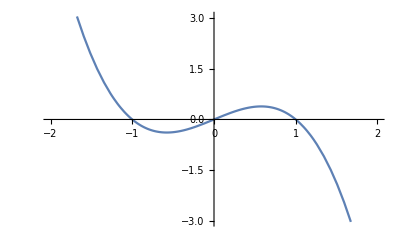

```mathematica
(* plot drift function*)
Plot[myDrift[x],{x,-2,2}]
```